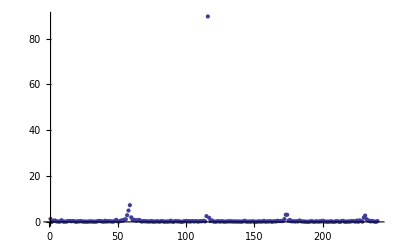

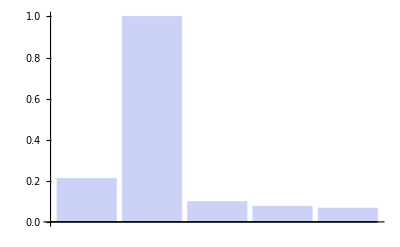

{{1,0.211531},{2,1.},{3,0.0986874},{4,0.0761641},{5,0.0673224}}

```mathematica
(*Specify folder structure and filenames*)
Clear[ Filename, Filepath, rawData, partitionedData, partitionedData2, ArrayUnitsToMM, UnitsToMM];
Filename = "F0017CH1";
Filepath = NotebookDirectory[]<>"../data/fourier/";
(*Import raw Data, still needs to be cleaned and re-ordered*)
rawData = Import[Filepath<> Filename <> ".csv"];

rawData = Flatten[rawData];
(*Ignore first 2 lines (metadata) and re-order it by x-value first and y-value scond*)
fourier = Abs[Fourier[rawData]];

ListPlot[Take[fourier,240],PlotRange->All]
fourier = Map[Total[Take[fourier,{#*58-3, #*58+3}]]&, Range[5]];
fourier = fourier / Max[fourier];
BarChart[fourier,PlotRange->All]
fourier = MapIndexed[{#2[[1]], Round[#1, 0.001]}&,fourier]

path = Filepath  <> Filename <> "-Furier"<>".txt";
Export[path,fourier, "Table"];
```